```mathematica
SetOptions[SelectedNotebook[],NotebookAutoSave->True](*save notebook after each evaluation*)
```

## Spherical Harmonic Functions

```mathematica
Y[l_,m_,θ_,ϕ_]:=SphericalHarmonicY[l,m,θ,ϕ]
```

```mathematica
(*print the first few spherical harmonic functions*)
lmax=2;
Grid[Prepend[Table[Prepend[Table[If[Abs[m]<=l,SphericalHarmonicY[l,m,θ,ϕ],""],{m,-lmax,lmax}],Row[{"l = ",l}]],{l,0,lmax}],Join[{""},Table[Row[{"m = ",m}],{m,-lmax,lmax}]]],Frame->All]
```

```mathematica
(*check eigenvalue equations*)
Lz[f_]:=-I*ħ*D[f,ϕ]
L2[f_]:=-ħ^2*(1/Sin[θ]*D[Sin[θ]*D[f,θ],θ]+1/Sin[θ]^2*D[f,{ϕ,2}])
```

```mathematica
ll=4;mm=2;(*replace with different values of l and m*)
Simplify[L2[Y[ll,mm,θ,ϕ]]-ħ^2*ll*(ll+1)*Y[ll,mm,θ,ϕ]]
Simplify[Lz[Y[ll,mm,θ,ϕ]]-ħ*mm*Y[ll,mm,θ,ϕ]]
```

## Example 7.5, McIntyre

#### Free particle constrained to the surface of a sphere. The energy depends on the eigenvalues of L^2.

```mathematica
(*angular wave function on a unit sphere*)
psi1[θ_,ϕ_]:=√(60060/(139301Pi))(1/4+Cos[2θ]^3+Sin[ϕ]^2);
```

```mathematica
(*check normalization*)
NIntegrate[Conjugate[psi1[θ,ϕ]]*psi1[θ,ϕ]*Sin[θ],{θ,0,Pi},{ϕ,0,2Pi}]
```

1.

```mathematica
(*compute the coefficients in the spherical harmonic expansion*)
(*clm[{l,m}] = Integrate[Conjugate[Y[l,m,θ,ϕ]]*psi1[θ,ϕ]*Sin[θ],{θ,0,Pi},{ϕ,0,2 Pi}]]*)
lmax=6;
clm=Association@Flatten[
Table[
Rule[{l,m},
Integrate[Conjugate[Y[l,m,θ,ϕ]]*psi1[θ,ϕ]*Sin[θ],{θ,0,Pi},{ϕ,0,2 Pi}]],
{l,0,lmax},{m,-l,l}],1];
```

```mathematica
(*print out a table of the coefficients*)
Grid[Prepend[Table[Prepend[Table[If[Abs[m]<=l,clm[{l,m}]],{m,-lmax,lmax}],Row[{"l = ",l}]],{l,0,lmax}],Join[{""},Table[Row[{"m = ",m}],{m,-lmax,lmax}]]],Frame->All]
```

| m = -6 | m = -5 | m = -4 | m = -3 | m = -2 | m = -1 | m = 0 | m = 1 | m = 2 | m = 3 | m = 4 | m = 5 | m = 6
l = 0 |  |  |  |  |  |  | 69 √(429/4875535) |  |  |  |  |  | 
l = 1 |  |  |  |  |  | 0 | 0 | 0 |  |  |  |  | 
l = 2 |  |  |  |  | -5 √(1001/278602) | 0 | 80 √(143/2925321) | 0 | -5 √(1001/278602) |  |  |  | 
l = 3 |  |  |  | 0 | 0 | 0 | 0 | 0 | 0 | 0 |  |  | 
l = 4 |  |  | 0 | 0 | -√(3003/278602) | 0 | -128 √(39/53630885) | 0 | -√(3003/278602) | 0 | 0 |  | 
l = 5 |  | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 
l = 6 | 0 | 0 | 0 | 0 | -(13 √(11/139301))/2 | 0 | 512 √(5/32178531) | 0 | -(13 √(11/139301))/2 | 0 | 0 | 0 | 0

```mathematica
(*compute |clm|^2 = probability to find particle with energy Subscript[E, l]*)
probs=Total[Table[Abs[clm[{l,m}]]^2,{l,0,lmax},{m,-l,l}],{2}]
```

{2042469/4875535,0,1440725/2925321,0,1795131/53630885,0,3050869/64357062}

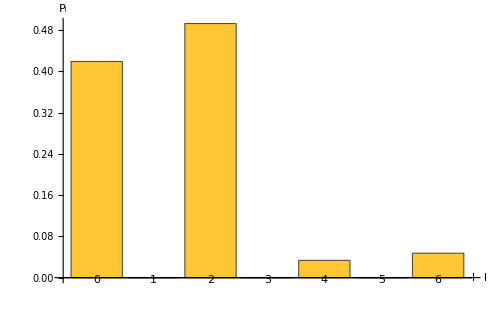

```mathematica
(*print histogram using BarChart*)
BarChart[probs,AxesLabel->{"l","P_l"},ChartLabels->{"0","1","2","3","4","5","6"},BaseStyle->{18},ImageSize->500]
```

```mathematica
(*truncated expansion in terms of spherical harmonics*)
PSI1[θ_,ϕ_]:=Sum[clm[{l,m}]*Y[l,m,θ,ϕ],{l,0,lmax},{m,-l,l}];
```

```mathematica
(*compare wave functions using radial distortion plots*)
SphericalPlot3D[Abs[psi1[θ,ϕ]]^2,{θ,0,Pi},{ϕ,0,2 Pi},PlotPoints->50,Mesh->None,PlotRange->All]
SphericalPlot3D[Abs[PSI1[θ,ϕ]]^2,{θ,0,Pi},{ϕ,0,2 Pi},PlotPoints->50,Mesh->None]
```

```mathematica
(*compare wave functions by computing absolute square of inner product*)
Abs[NIntegrate[Conjugate[psi1[θ,ϕ]]*PSI1[θ,ϕ]*Sin[θ],{θ,0,Pi},{ϕ,0,2 Pi}]]^2
```

0.984661